```mathematica
Y=(*L{Cos[τ]Cosh[ρ],Sin[ϕ]Sinh[ρ],Cos[ϕ]Sinh[ρ],Sin[τ]Cosh[ρ]};*)(*{L/z t,(L^2e^r+e^-r(t^2-z^2))/(2z),(L^2e^r-e^-r(t^2-z^2))/(2z)}*)
{L/z t,L/z x,(L^2+(t^2-x^2-z^2))/(2z),(L^2-(t^2-x^2-z^2))/(2z)}

X=(*{τ,ρ,ϕ,L}*){t,x,z,L}; 
pX=(*{pτ,pρ,pϕ,pL}*){pt,px,pz,pL};
dX=(*{dτ,dρ,dϕ,dL}*){dt,dx, dz,dL};
act[A_,B_]:=(A/.{pt->D[B,t],px->D[B,x],pz->D[B,z],pL->D[B,L]});

X0=X/.L->0;

ηA=DiagonalMatrix[{-1,1,1,-1}];

(*ds=D[Y,{{t,xi,z}}].{dt, dxi,dz};
ds2=FullSimplify[ds.ηA.ds]*)
dsL=D[Y,{X}].dX;
ds2=FullSimplify[dsL.ηA.dsL](*/.dL->0*)

J=D[Y,{X}];Jinv=FullSimplify[Inverse[J]];
ηL=FullSimplify[Jᵀ.ηA.J];

pdY=(pX.Jinv);
M=FullSimplify[{pdY}ᵀ.{ηA.Y}-({pdY}ᵀ.{ηA.Y})ᵀ];
KL=z^2/L^3FullSimplify[X0.ηL.X0 pX-2ηL.X0 X0.pX];
Act[A_,B_]:=FullSimplify[act[A,B]];
Comm[A_,B_]:=FullSimplify[act[A,B]-act[B,A]];(*(A/.{pt->D[B,t],pz->D[B,z]})-(B/.{pt->D[A,t],pz->D[A,z]})]*)

ηL//TraditionalForm
KL//TraditionalForm
M//TraditionalForm
```

{(L t)/z,(L x)/z,(L^2+t^2-x^2-z^2)/(2 z),(L^2-t^2+x^2+z^2)/(2 z)}

(-dt^2 L^2+dx^2 L^2+2 dL dt L t-2 dL dx L x+dL^2 (-t^2+x^2)+dz L (dz L-2 dL z))/z^2

(-L^2/z^2 | 0 | 0 | (L t)/z^2
0 | L^2/z^2 | 0 | -(L x)/z^2
0 | 0 | L^2/z^2 | -L/z
(L t)/z^2 | -(L x)/z^2 | -L/z | (x^2-t^2)/z^2)

{(pt (t^2+x^2+z^2)+2 t (px x+pz z))/L,-(2 x (pt t+pz z)+px (t^2+x^2-z^2))/L,-(2 z (pt t+px x)+pz (t^2-x^2+z^2))/L,((-t^2+x^2+z^2) (L pL+2 (pt t+px x+pz z)))/L^2}

(0 | px t+pt x | (pt L^2-2 t (px x+pz z)-pt (t^2+x^2+z^2))/(2 L) | -(pt L^2+2 t (px x+pz z)+pt (t^2+x^2+z^2))/(2 L)
-px t-pt x | 0 | (px L^2+2 x (pt t+pz z)+px (t^2+x^2-z^2))/(2 L) | (-px L^2+2 x (pt t+pz z)+px (t^2+x^2-z^2))/(2 L)
(-pt L^2+2 t (px x+pz z)+pt (t^2+x^2+z^2))/(2 L) | -(px L^2+2 x (pt t+pz z)+px (t^2+x^2-z^2))/(2 L) | 0 | pt t+px x+pz z
(pt L^2+2 t (px x+pz z)+pt (t^2+x^2+z^2))/(2 L) | (px L^2-2 x (pt t+pz z)-px (t^2+x^2-z^2))/(2 L) | -pt t-px x-pz z | 0)

```mathematica
Y.ηA.Y
```

-(L^2 t^2)/z^2+(L^2 x^2)/z^2+((L^2+t^2-x^2-z^2)^2)/(4 z^2)-((L^2-t^2+x^2+z^2)^2)/(4 z^2)

```mathematica
Simplify[Y.ηA.Y]
```

-L^2

```mathematica
Y
```

{t √(e+L^2/z^2),(√(e+L^2/z^2) (L^2+t^2-z^2))/(2 z),(√(e+L^2/z^2) (L^2-t^2+z^2))/(2 z)}

```mathematica
DSolve[z'[r]==r^2/((r-m)^2-Δr^2/4),z[r],r]
```

{{z[r]→C[1]+4 (r/4-((4 m^2+Δr^2) ArcTanh[(2 (-m+r))/Δr])/(8 Δr)+1/4 m Log[4 m^2-8 m r+4 r^2-Δr^2])}}

```mathematica
Solve[c+4 (r/4-((4 m^2+Δr^2) ArcTanh[(2 (-m+r))/Δr])/(8 Δr)+1/4 m Log[4 m^2-8 m r+4 r^2-Δr^2])==z,r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[c+4 (r/4-((4 m^2+Δr^2) ArcTanh[(2 (-m+r))/Δr])/(8 Δr)+1/4 m Log[4 m^2-8 m r+4 r^2-Δr^2])==z,r]

```mathematica
Simplify[4 (r/4-((4 m^2+Δr^2) ArcTanh[(2 (-m+r))/Δr])/(8 Δr)+1/4 m Log[4 m^2-8 m r+4 r^2-Δr^2])/.Δr->2Sqrt[m^2-Q^2]]
```

```mathematica
((-2 m^2+Q^2) ArcTanh[(-m+r)/(√(m^2-Q^2))]+√(m^2-Q^2) (r+m Log[4 (Q^2-2 m r+r^2)]))/(√(m^2-Q^2))
```

```mathematica
(4 m^2+Δr^2)/(2Δr)ArcTanh[(-m+r)/(Δr/2)]+r+m Log[4 Δ]+r+( m^2+Δr^2/4)/Δr Log[-(r-SubMinus[r])/(r-SubPlus[r])]+m Log[4 Δ]//TraditionalForm
```

((Δr^2/4+m^2) log(-(r-r_-)/(r-r_+)))/Δr+((Δr^2+4 m^2) tanh^-1((2 (r-m))/Δr))/(2 Δr)+2 m log(4 Δ)+2 r

```mathematica
Simplify[(1+bb)/(1-bb)/.bb->(-m+r)/(Δr/2)]
```

(-2 m+2 r+Δr)/(2 m-2 r+Δr)

```mathematica
%//TraditionalForm
```

{{z(r)→c_1+4 (1/4 m log(-Δr^2+4 m^2-8 m r+4 r^2)-((Δr^2+4 m^2) tanh^-1((2 (r-m))/Δr))/(8 Δr)+r/4)}}

```mathematica
ηInv=FullSimplify[Inverse[ηL]]
```

{{-(t^2+z^2)/L^2,-(t x)/L^2,-(t z)/L^2,-t/L},{-(t x)/L^2,(-x^2+z^2)/L^2,-(x z)/L^2,-x/L},{-(t z)/L^2,-(x z)/L^2,0,-z/L},{-t/L,-x/L,-z/L,-1}}

```mathematica
act[A_,B_]:=(A/.{pt->D[B,t],px->D[B,x],pz->D[B,z],pL->D[B,L]});
```

```mathematica
%//TraditionalForm
```

(-(t^2+z^2)/L^2 | -(t x)/L^2 | -(t z)/L^2 | -t/L
-(t x)/L^2 | (z^2-x^2)/L^2 | -(x z)/L^2 | -x/L
-(t z)/L^2 | -(x z)/L^2 | 0 | -z/L
-t/L | -x/L | -z/L | -1)

```mathematica
act[pX,A[X]]
```

{A^({1,0,0,0})[{t,x,z,L}],A^({0,1,0,0})[{t,x,z,L}],A^({0,0,1,0})[{t,x,z,L}],A^({0,0,0,1})[{t,x,z,L}]}

```mathematica
Act[(Det[ηL]ηInv.pX),A[X]][[2]]
```

-1/z^6 L^4 (L x A^({0,0,0,1})[{t,x,z,L}]+x z A^({0,0,1,0})[{t,x,z,L}]+(x-z) (x+z) A^({0,1,0,0})[{t,x,z,L}]+t x A^({1,0,0,0})[{t,x,z,L}])

```mathematica
Det[ηL]
```

L^6/z^6

```mathematica
Lapl=FullSimplify[z^3/L^3Sum[ act[pX[[i]],act[(L^3/z^3 ηInv.pX),A[X]][[i]]],{i,1,4}]]
```

-A^({0,0,0,2})[{t,x,z,L}]-1/L^2(3 L A^({0,0,0,1})[{t,x,z,L}]+4 z A^({0,0,1,0})[{t,x,z,L}]+2 L z A^({0,0,1,1})[{t,x,z,L}]+3 x A^({0,1,0,0})[{t,x,z,L}]+2 L x A^({0,1,0,1})[{t,x,z,L}]+2 x z A^({0,1,1,0})[{t,x,z,L}]+x^2 A^({0,2,0,0})[{t,x,z,L}]-z^2 A^({0,2,0,0})[{t,x,z,L}]+3 t A^({1,0,0,0})[{t,x,z,L}]+2 L t A^({1,0,0,1})[{t,x,z,L}]+2 t z A^({1,0,1,0})[{t,x,z,L}]+2 t x A^({1,1,0,0})[{t,x,z,L}])-((t^2+z^2) A^({2,0,0,0})[{t,x,z,L}])/L^2

```mathematica
D[A[X], {t,2}]
```

A^({2,0,0,0})[{t,x,z,L}]

```mathematica
Simplify[Lapl-z^2/L^2(-D[A[X], {t,2}]+D[A[X], {x,2}])+1/L^2(act[X.pX,act[X.pX,A[X]]]+2act[X.pX,A[X]])]
```

(z (-A^({0,0,1,0})[{t,x,z,L}]+z A^({0,0,2,0})[{t,x,z,L}]))/L^2

```mathematica
%//TraditionalForm
```

-((t^2+z^2) A^({2,0,0,0})({t,x,z,L}))/L^2-1/L^2(x^2 A^({0,2,0,0})({t,x,z,L})-z^2 A^({0,2,0,0})({t,x,z,L})+3 x A^({0,1,0,0})({t,x,z,L})+2 L x A^({0,1,0,1})({t,x,z,L})+2 x z A^({0,1,1,0})({t,x,z,L})+2 t x A^({1,1,0,0})({t,x,z,L})+3 L A^({0,0,0,1})({t,x,z,L})+4 z A^({0,0,1,0})({t,x,z,L})+2 L z A^({0,0,1,1})({t,x,z,L})+3 t A^({1,0,0,0})({t,x,z,L})+2 L t A^({1,0,0,1})({t,x,z,L})+2 t z A^({1,0,1,0})({t,x,z,L}))-A^({0,0,0,2})({t,x,z,L})

```mathematica
%/.
```

```mathematica
(-dt^2 L^2+dx^2 L^2+2 dL dt L t-2 dL dx L x+dL^2 (-t^2+x^2)+dz L (dz L-2 dL z))/z^2
```

(-dt^2 L^2+dx^2 L^2+dz^2 L^2)/z^2

```mathematica
Det[ηL]
```

L^6/z^6

```mathematica
ηL//TraditionalForm
```

(-L^2/z^2 | 0 | (L t)/z^2
0 | L^2/z^2 | -L/z
(L t)/z^2 | -L/z | -t^2/z^2)

```mathematica
Det[ηL]
```

L^4/z^4

```mathematica
ds2//TraditionalForm
```

(dL^2 (x^2-t^2)+2 dL dt L t-2 dL dx L x+dz L (dz L-2 dL z)-dt^2 L^2+dx^2 L^2)/z^2

```mathematica
(-dt^2 L^2+2 dL dt L t-dL^2 t^2+dz L (dz L-2 dL z))/z^2/.dL->0
```

(-dt^2 L^2+dz^2 L^2)/z^2

```mathematica
Y={Sqrt[L^2/z^2+e] t,(L^2+e z^2+(t^2-z^2+c z))/(2z),(L^2+e z^2-(t^2-z^2+c z))/(2z)}
dsL=D[Y,{X}].dX;
ds2=FullSimplify[dsL.ηA.dsL]/.dL->0
FullSimplify[Y.ηA.Y]
```

{t √(e+L^2/z^2),(L^2+t^2+c z-z^2+e z^2)/(2 z),(L^2-t^2-c z+z^2+e z^2)/(2 z)}

(2 dt dz e t z (L^2+e z^2)-dt^2 (L^2+e z^2)^2+dz^2 (L^4-e^2 z^2 (t^2+z^2)))/(z^2 (L^2+e z^2))

((c-z) (L^2+e z^2))/z

```mathematica
FullSimplify[%]
```

-L^2-e z^2

```mathematica
KL[[1]]
```

(2 pz t z+pt (t^2+z^2))/L

```mathematica
Comm[pt t+pz z,L^3/z^2 KL[[1]]]
```

-(L^2 (2 pz t z+pt (t^2+z^2)))/z^2

```mathematica
{Comm[pt t+pz z, KL[[1]]],Comm[L pt, KL[[1]]],Comm[pt t+pz z, L pt]}
{Comm[pt t+pz z, L^3/z^2 KL[[1]]],Comm[L pt, L^3/z^2 KL[[1]]],Comm[pt t+pz z,L pt]}
```

{(2 pz t z+pt (t^2+z^2))/L,2 (pt t+pz z),-L pt}

{-(L^2 (2 pz t z+pt (t^2+z^2)))/z^2,(2 L^3 (pt t+pz z))/z^2,-L pt}

```mathematica
{Comm[(pt t+pz z), L^3/z^2 KL[[1]]],Comm[L pt, L^3/z^2 KL[[1]]],Comm[pt t+pz z,L pt]}
```

{-(L^2 (2 pz t z+pt (t^2+z^2)))/z^2,(2 L^3 (pt t+pz z))/z^2,-L pt}

```mathematica
R=m+Sqrt[1/(z^2-Δr^2)+Δr^2]
```

m+√(Δr^2+1/(z^2-Δr^2))

```mathematica
FullSimplify[D[R,z]]
```

-z/((z^2-Δr^2)^2 √(Δr^2+1/(z^2-Δr^2)))

```mathematica
FullSimplify[%^2 R^2/((R-m)^2-Δr^2)]
```

(z^2 (m+√(Δr^2+1/(z^2-Δr^2)))^2)/((z^2-Δr^2)^2 (1+z^2 Δr^2-Δr^4))

```mathematica
((R-m)^2-Δr^2)/R^2
```

1/((z^2-Δr^2) (m+√(Δr^2+1/(z^2-Δr^2)))^2)

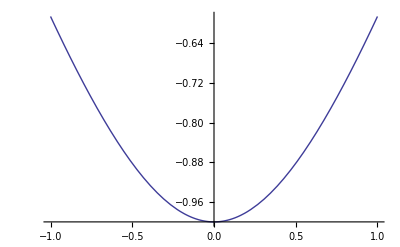

```mathematica
Plot[Sqrt[x^2+1]-2,{x,-1,1}]
```

```mathematica
Integrate[1/(r^2-c^2),r,Assumptions-> {c∈Reals&& r>Abs[c]}]
```

-ArcTanh[r/c]/c

```mathematica
D[-ArcCoth[r/c]/c,r]
```

-1/(c^2 (1-r^2/c^2))

```mathematica
Series[-Δr/2 Coth[Δr/(2m^2)z],{z,0,4}]
```

-m^2/z-(Δr^2 z)/(12 m^2)+(Δr^4 z^3)/(720 m^6)+O[z]^5

```mathematica
(m^2/z+(Δr^2 z)/(12 m^2))^2-Δr^2/4
```

-Δr^2/4+(m^2/z+(z Δr^2)/(12 m^2))^2

```mathematica
FullSimplify[%]
```

-Δr^2/4+(m^2/z+(z Δr^2)/(12 m^2))^2

```mathematica
Det[ηL]
```

L^4/z^4

```mathematica
Comm[pt t+pz z,pt]
```

-pt

```mathematica
Comm[pt,L^3/ z^2 KL[[1]]]
```

(2 L^2 (pt t+pz z))/z^2

```mathematica
Act[pL,Det[ηL]Inverse[ηL].pX]
```

{-(L (3 L pL t+2 (pz t z+pt (t^2+z^2))))/z^4,-(L (3 L pL+2 pt t))/z^3,-(L^2 (4 L pL+3 pt t+3 pz z))/z^4}

```mathematica
Jinvᵀ//TraditionalForm
```

((t^2+z^2)/(L z) | (2 t)/L | t/z
-(t (L^2+t^2+z^2))/(2 L^2 z) | -t^2/L^2-1 | -(L^2+t^2-z^2)/(2 L z)
-(t (-L^2+t^2+z^2))/(2 L^2 z) | 1-t^2/L^2 | (L^2-t^2+z^2)/(2 L z))

```mathematica
FullSimplify[Y.Jinvᵀ.pX]
```

L pL+pt t+pz z

```mathematica
Det[ηL]
```

L^4/z^4

```mathematica
FullSimplify[act[L pL+pt t+pz z,act[L pL+pt t+pz z, f[t,z]]] ]
```

z f^(0,1)[t,z]+z^2 f^(0,2)[t,z]+t (f^(1,0)[t,z]+2 z f^(1,1)[t,z]+t f^(2,0)[t,z])

```mathematica
FullSimplify[act[L pL+pt t+pz z,act[L pL+pt t+pz z, f[t,z,L]]] ]
```

L f^(0,0,1)[t,z,L]+L^2 f^(0,0,2)[t,z,L]+z f^(0,1,0)[t,z,L]+2 L z f^(0,1,1)[t,z,L]+z^2 f^(0,2,0)[t,z,L]+t f^(1,0,0)[t,z,L]+2 L t f^(1,0,1)[t,z,L]+2 t z f^(1,1,0)[t,z,L]+t^2 f^(2,0,0)[t,z,L]

```mathematica
act[A_,B_]:=(A/.{pu->D[B,u],pρ->D[B,ρ],pv->D[B,v]});
```

```mathematica
{Lm,Lp}=I{E^(-I u),E^(I u)}(Coth[2ρ]pu-1/Sinh[2ρ] pv)+I{E^(-I u)I/2 pρ,-E^(I u)I/2 pρ}
```

{-1/2 ⅇ^(-ⅈ u) pρ+ⅈ ⅇ^(-ⅈ u) (pu Coth[2 ρ]-pv Csch[2 ρ]),1/2 ⅇ^(ⅈ u) pρ+ⅈ ⅇ^(ⅈ u) (pu Coth[2 ρ]-pv Csch[2 ρ])}

```mathematica
Comm[Lm,Lp]
```

-2 ⅈ pu

```mathematica
FullSimplify[M[[1,3]]-1/(2L)(-L^2pt- KL[[1]])]
```

0

```mathematica
fY[q_,r_,s_]:=Y/.{τ->q,ρ->r,ϕ->s}
```

```mathematica
Simplify[(fY[t1,r1,f1]-fY[t2,r2,f2]).ηA.(fY[t1,r1,f1]-fY[t2,r2,f2])]
```

2 L^2 (-1+Cos[t1-t2] Cosh[r1] Cosh[r2]-Cos[f1-f2] Sinh[r1] Sinh[r2])

```mathematica
FullSimplify[fY[t2,r2,f2].ηA.fY[t1,r1,f1]]
```

L^2 (-Cos[t1-t2] Cosh[r1] Cosh[r2]+Cos[f1-f2] Sinh[r1] Sinh[r2])

```mathematica
FullSimplify[Series[fY[t2,r2,f2].ηA.fY[t1,r1,f1],{t1,t2,2},{f1,f2,2}]]
```

(-L^2 Cosh[r1-r2]-1/2 (L^2 Sinh[r1] Sinh[r2]) (f1-f2)^2+O[f1-f2]^3)+1/2 L^2 Cosh[r1] Cosh[r2] (t1-t2)^2+O[t1-t2]^3

```mathematica
FullSimplify[Series[-L^2 Cosh[r1-r2]-1/2 (L^2 Sinh[r1] Sinh[r2]) (f1-f2)^2+1/2 L^2 Cosh[r1] Cosh[r2] (t1-t2)^2,{r1,r2,2}]]
```

1/2 L^2 (-2+(t1-t2)^2 Cosh[r2]^2-(f1-f2)^2 Sinh[r2]^2)+1/2 L^2 (-(f1-f2)^2+(t1-t2)^2) Cosh[r2] Sinh[r2] (r1-r2)+1/4 L^2 (-2+(t1-t2)^2 Cosh[r2]^2-(f1-f2)^2 Sinh[r2]^2) (r1-r2)^2+O[r1-r2]^3

```mathematica
1/2 L^2 (-2+(t1-t2)^2 Cosh[r2]^2-(f1-f2)^2 Sinh[r2]^2)+1/2 L^2 (-(f1-f2)^2+(t1-t2)^2) Cosh[r2] Sinh[r2] (r1-r2)+1/4 L^2 (-2+(t1-t2)^2 Cosh[r2]^2-(f1-f2)^2 Sinh[r2]^2) (r1-r2)^2
```

```mathematica
Asymptotic
```

## Commutators

The trick is to replace the momenta with the derivative of the operator we want to act on. This does not affect the momenta inside the operator we act on.

```mathematica
Comm[M[[1,2]],M[[1,3]]]
```

-pt t-pz z

```mathematica
FullSimplify[Act[M[[2,3]],(z)^(-m+n) y^m/((z)^2+(t-y)^2)^n]]
```

-y^m z^(-m+n) ((t-y)^2+z^2)^(-1-n) ((t-y) (m (t-y)+n (t+y))+(m+n) z^2)

```mathematica
FullSimplify[Act[M[[2,3]],(z)^(-m+n) y^m/((z)^2+(t-y)^2)^n/.m->0]]
```

-n z^n ((t-y)^2+z^2)^(-1-n) (t^2-y^2+z^2)

```mathematica
Y[[3]]
```

1/2 (1+(L^2-t^2)/z^2) z

```mathematica
FullSimplify[(KL[[1]]/.{pt->D[Y[[1]],t],pz->D[Y[[1]],z]})-Y[[3]]+Y[[2]]]
```

0

```mathematica
FullSimplify[Y[[2]]-Y[[3]]]
```

(e^-r (t-z) (t+z))/z

## Invariant subspace

The invariant subspace is spanned by Y_i, Y_-. So at each point the value of Y_+ defines this space. (only D changes Y_+)

```mathematica
{Yp=FullSimplify[Y[[2]]+Y[[3]]],Ym=FullSimplify[Y[[2]]-Y[[3]]]}
```

{L^2/z,t^2/z-z}

```mathematica
Show[ParametricPlot3D[{Y/.L->1,-Y/.L->1},{z,.2,4},{t,-5,5},PlotRange->{{-3,3},{-3,3},{-3,3}},Mesh->None,PlotStyle-> {Blue,Red}],Plot3D[1-y,{x,-3,3},{y,-3,3}]]
```

-Graphics3D-

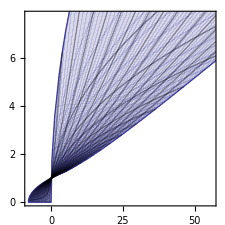

```mathematica
ParametricPlot[{Y[[2]]-Y[[3]],Y[[1]]}/.{L->1},{t,0,10},{z,.1,8},AspectRatio->1]
```

## Laplacian